Piecewise[{{2 ⅇ^(-2 x), x≥0}, {0, True}}]

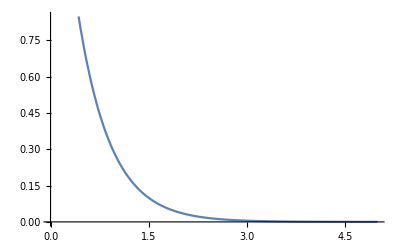

```mathematica
intensity=2;
exponentialPDF=PDF[ExponentialDistribution[intensity],x]
Plot[exponentialPDF,{x,0,5}]
```

1-(Piecewise[{{1-ⅇ^(-2 x), x≥0}, {0, True}}])

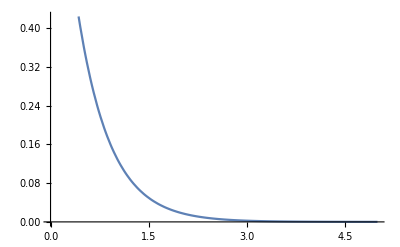

```mathematica
exponentialTailDistribution=1-CDF[ExponentialDistribution[intensity],x]
Plot[exponentialTailDistribution,{x,0,5}]
```

(1-(Piecewise[{{1-ⅇ^(-2 x), x≥0}, {0, True}}]))^3

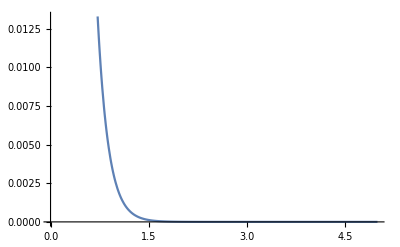

3 (1-(Piecewise[{{1-ⅇ^(-2 x), x≥0}, {0, True}}]))^2 (Piecewise[{{0, x<0}, {2-2 ⅇ^(-2 x) (-1+ⅇ^(2 x)), x>0}, {Indeterminate, True}}])

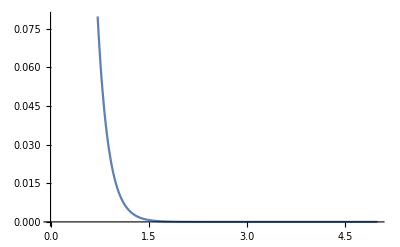

```mathematica
seriesTailDistribution=exponentialTailDistribution^3
Plot[seriesTailDistribution,{x,0,5}]
seriesPDF=D[1-seriesTailDistribution,x]
Plot[seriesPDF,{x,0,5}]
```

```mathematica
CalculateSystemLifetimePDF[reliabilityFunction_,componentsDistributions_]:=[

]
```

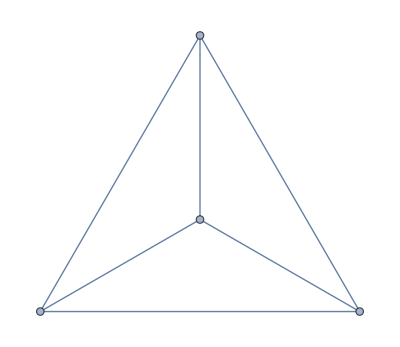

{{1,2},{1,4,2},{1,3,2},{1,4,3,2},{1,3,4,2}}

```mathematica
g=CompleteGraph[4]
paths=FindPath[g,1,2,Infinity,All]
```

```mathematica
replaceVertexNumbersWithRandomVariables[path_,distributions_]:= distributions[[#]]&/@path;

distributions={x1,x2,x3,x4};
replaceVertexNumbersWithRandomVariables[{1,2},distributions]
```

{x1,x2}

```mathematica
distributions={x1,x2,x3,x4};
paths={{1,2},{1,4,2},{1,3,2},{1,4,3,2},{1,3,4,2}};
randomVariablePaths=replaceVertexNumbersWithRandomVariables[#,distributions]&/@paths;
multipliedoutPaths=Apply[Times,randomVariablePaths,{1}];
structureFunction=1-Apply[Times,1-multipliedoutPaths]
Expand[structureFunction]
Expand[structureFunction]/.a_^p_:>a (*remove powers*)
```

1-(1-x1 x2) (1-x1 x2 x3) (1-x1 x2 x4) (1-x1 x2 x3 x4)^2

x1 x2+x1 x2 x3-x1^2 x2^2 x3+x1 x2 x4-x1^2 x2^2 x4+2 x1 x2 x3 x4-3 x1^2 x2^2 x3 x4+x1^3 x2^3 x3 x4-2 x1^2 x2^2 x3^2 x4+2 x1^3 x2^3 x3^2 x4-2 x1^2 x2^2 x3 x4^2+2 x1^3 x2^3 x3 x4^2-x1^2 x2^2 x3^2 x4^2+3 x1^3 x2^3 x3^2 x4^2-2 x1^4 x2^4 x3^2 x4^2+x1^3 x2^3 x3^3 x4^2-x1^4 x2^4 x3^3 x4^2+x1^3 x2^3 x3^2 x4^3-x1^4 x2^4 x3^2 x4^3-x1^4 x2^4 x3^3 x4^3+x1^5 x2^5 x3^3 x4^3

x1 x2

a b c

```mathematica
Expand[1-(1-x1 x2) (1-x1 x2 x3) (1-x1 x2 x4) (1-x1 x2 x3 x4)^2]
```

x1 x2+x1 x2 x3-x1^2 x2^2 x3+x1 x2 x4-x1^2 x2^2 x4+2 x1 x2 x3 x4-3 x1^2 x2^2 x3 x4+x1^3 x2^3 x3 x4-2 x1^2 x2^2 x3^2 x4+2 x1^3 x2^3 x3^2 x4-2 x1^2 x2^2 x3 x4^2+2 x1^3 x2^3 x3 x4^2-x1^2 x2^2 x3^2 x4^2+3 x1^3 x2^3 x3^2 x4^2-2 x1^4 x2^4 x3^2 x4^2+x1^3 x2^3 x3^3 x4^2-x1^4 x2^4 x3^3 x4^2+x1^3 x2^3 x3^2 x4^3-x1^4 x2^4 x3^2 x4^3-x1^4 x2^4 x3^3 x4^3+x1^5 x2^5 x3^3 x4^3

```mathematica
getStructureFunction[x1_,x2_,x3_,x4_]:=[
structureFunction=
]
```

```mathematica
v={1,4,9,16,25,36,49,64,81,100}
v[[1]]
```

{1,4,9,16,25,36,49,64,81,100}

1